## Объявление глобальных переменных

```mathematica
print@x_:=(Print@x;x);
```

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 22.8377 | 0.22085
1000. | 0. | 48.5342 | 0.324504
2000. | 0. | 98.5757 | 0.454252
3000. | 0. | 149.486 | 0.546903
4000. | 0. | 199.729 | 0.631688
5000. | 0. | 250.886 | 0.73555
6000. | 0. | 300.269 | 0.782418
7000. | 0. | 352.02 | 0.787111
8000. | 0. | 400.772 | 0.89757
9000. | 0. | 449.476 | 0.961525
10000. | 0. | 497.687 | 1.06336

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-1.11748+0.0501363 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.11748 | 0.777848 | -1.43663 | 0.18466
x | 0.0501363 | 0.000131438 | 381.446 | 2.97761×10^-20

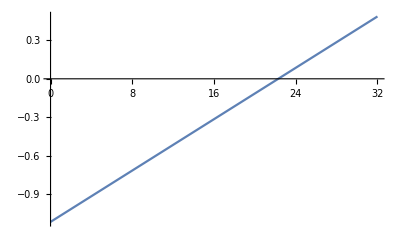

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit=LinearModelFit[forFit,{1,x},x]
fit@"ParameterTable"
Plot[fit["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit["FitResiduals"])/(print@forFitCr))^2
```

{-1.11294,-0.484615,-0.579385,0.194397,0.301691,1.32164,0.56908,2.18317,0.799023,-0.633442,-2.55862}

{0.22085,0.324504,0.454252,0.546903,0.631688,0.73555,0.782418,0.787111,0.89757,0.961525,1.06336}

{25.3952,2.23025,1.62682,0.126345,0.228097,3.2285,0.529016,7.69315,0.792467,0.434003,5.78956}

```mathematica
χ2=Total[(fit["FitResiduals"]/forFitCr)^2]/(11-2)
```

5.34149

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

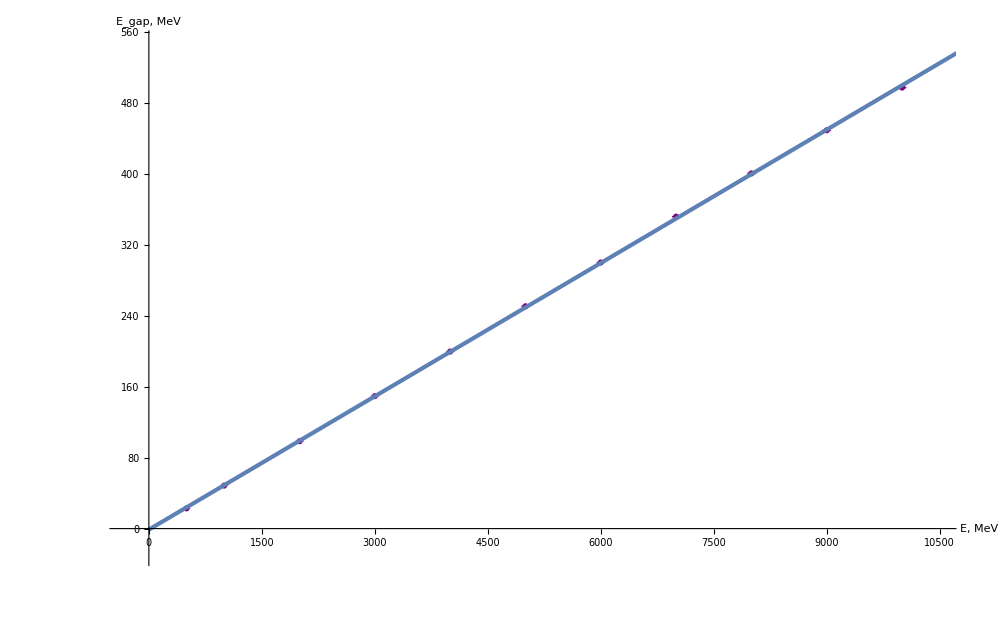

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res.png

```mathematica
plot =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,550}}], 
Plot[fit["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib.png",plot,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res.png",fit@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exp = {fit[0],fit[1]-fit[0], χ2};
exp//TableForm
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res.csv",exp,"CSV"]
```

-2.08265
0.0490596
2.54086

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
100. | 0. | 2.17421 | 0.239732
1000. | 0. | 45.8726 | 0.478714
2000. | 0. | 96.0239 | 0.744409
3000. | 0. | 145.268 | 0.844198
4000. | 0. | 195.018 | 1.02457
5000. | 0. | 244.115 | 1.06362
6000. | 0. | 294.698 | 1.19656
7000. | 0. | 339.521 | 1.27942
8000. | 0. | 390.362 | 1.3745
9000. | 0. | 440.857 | 1.50428
10000. | 0. | 486.364 | 1.6147

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-3.24479+0.0514355 x-1.26425×10^-7 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.24479 | 0.652957 | -4.96938 | 0.00109395
x | 0.0514355 | 0.00030217 | 170.221 | 1.58741×10^-15
x^2 | -1.26425×10^-7 | 2.84858×10^-8 | -4.43818 | 0.00217321

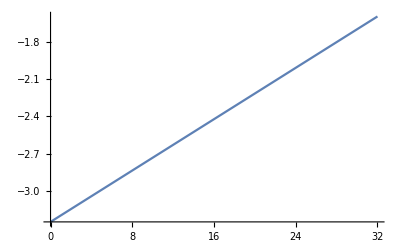

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
fit2@"Properties"
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
```

{0.396379,0.469923,-0.544775,-0.43807,-0.745003,0.113568,-0.547516,1.4109,0.623925,0.0414851,-0.780814}

{0.22085,0.324504,0.454252,0.546903,0.631688,0.73555,0.782418,0.787111,0.89757,0.961525,1.06336}

{3.22127,2.09707,1.43827,0.641605,1.39095,0.0238389,0.489685,3.21307,0.483201,0.0018615,0.539176}

```mathematica
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

1.6925

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

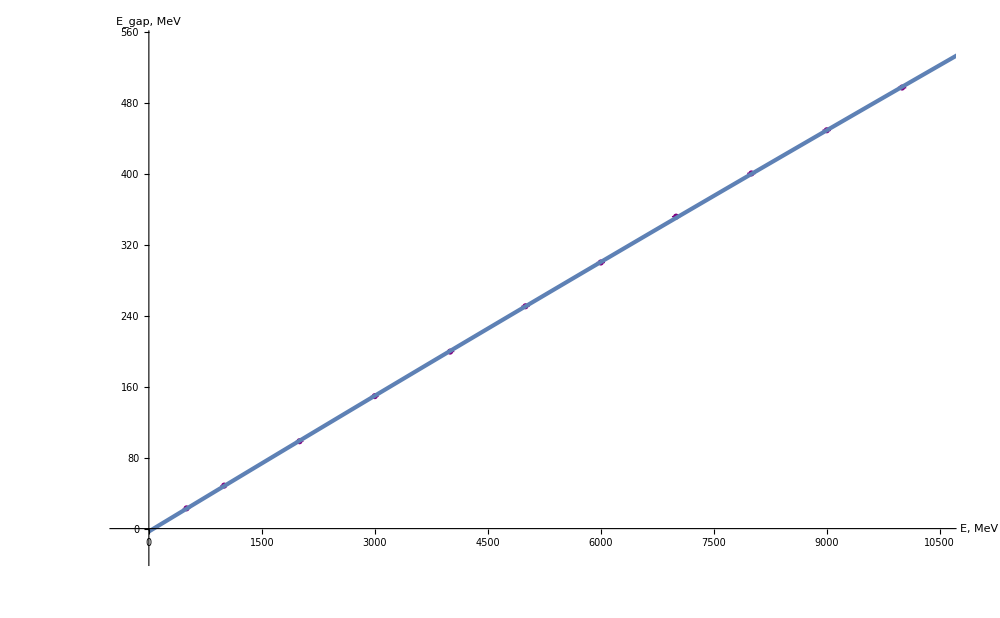

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib2.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,550}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/calib2.png",plot2,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

```mathematica
fit2[1] - fit2[0]
```

0.0500709

#### Экспорт фита данных в CSV формат

```mathematica
c = fit2[0]
b = fit2[1]-c
a = (fit2[10^7]-10^7*b-c)/10^14
```

-3.24479

0.0514354

-1.26425×10^-7

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
```

{{-3.24479,0.0514355,-1.26425×10^-7},{0.652957,0.00030217,2.84858×10^-8},1.6925}

```mathematica
exportE//TableForm
```

-3.24479 | 0.0514355 | -1.26425×10^-7
0.652957 | 0.00030217 | 2.84858×10^-8
1.6925 |  |

```mathematica
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2param.csv",fit2@"BestFitParameters","CSV"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2err.csv",fit2@"ParameterErrors","CSV"]
```

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2param.csv

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2err.csv

```mathematica
exp2 = {a,b,c, χ22};
exp2//TableForm
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2.csv",exportE,"CSV"]
```

-1.26425×10^-7
0.0514354
-3.24479
1.6925

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["/Users/kirillivanov/Documents/Code/For Geant analysis/log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
882.842 | 7.59596 | 0.213228 | 0.00434981
1367.03 | 9.54972 | 0.171137 | 0.00336989
1956.12 | 10.647 | 0.146962 | 0.00280206
2927.16 | 13.6248 | 0.114384 | 0.00216022
3535.84 | 15.2956 | 0.108444 | 0.00203765
4101.11 | 17.0461 | 0.101573 | 0.00190828
4951.12 | 17.956 | 0.0920119 | 0.00172132
6312.99 | 20.871 | 0.0816137 | 0.00151433
7163.25 | 21.4908 | 0.0782499 | 0.0014478
8033.74 | 22.5809 | 0.0756144 | 0.00139708
9745.9 | 27.7187 | 0.0702665 | 0.00133934

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00559905+6.13976/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00559905 | 0.00173068 | 3.23518 | 0.0102373
1/(√x) | 6.13976 | 0.0910907 | 67.4027 | 1.75897×10^-13

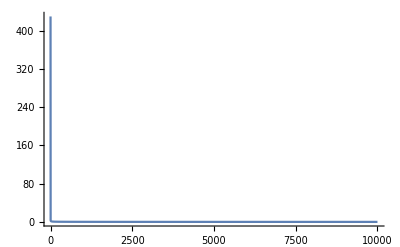

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
```

{0.000991061,-0.000521494,0.00254246,-0.00469706,-0.000408729,0.0000996796,-0.000844011,-0.00125941,0.00010776,0.00151514,0.00247461}

{0.00434981,0.00336989,0.00280206,0.00216022,0.00203765,0.00190828,0.00172132,0.00151433,0.0014478,0.00139708,0.00133934}

{0.0519111,0.023948,0.823294,4.72778,0.040236,0.00272853,0.240422,0.691667,0.00553978,1.17615,3.41378}

```mathematica
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

1.24416

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,5}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

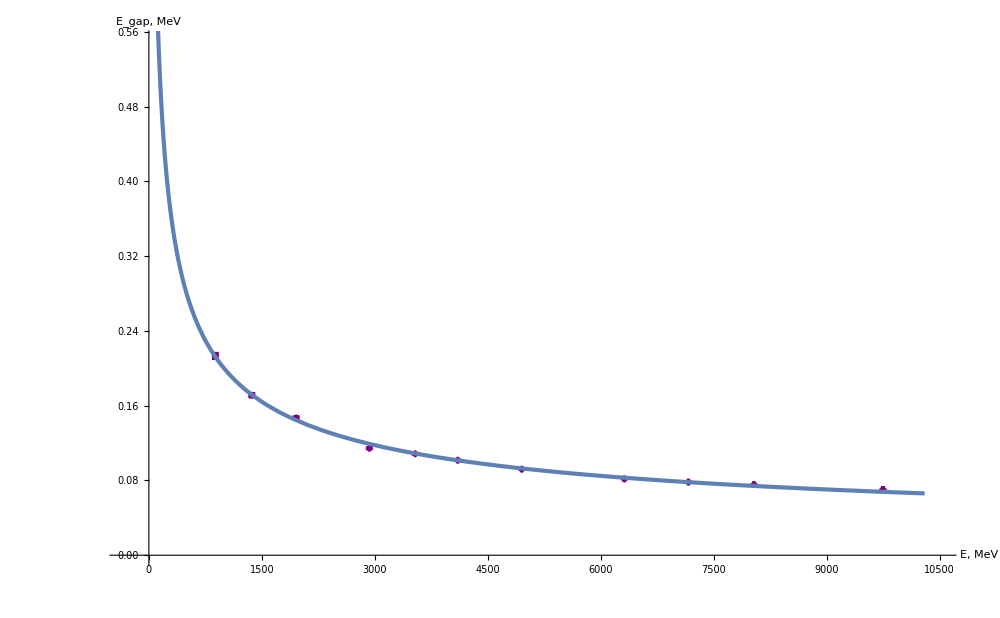

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/re.png

/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/re.png",plotR,"PNG"]
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
```

{{0.00559905,6.13976},{0.00173068,0.0910907},1.24416}

```mathematica
expR= {fitR[10^20],fitR[1]-fitR[10^20], χR};
expR//TableForm
Export["/Users/kirillivanov/Documents/Code/For Geant analysis/fit_re_res.csv",exportR,"CSV"]
```

0.00559905
6.13976
1.24416

/Users/kirillivanov/Documents/Code/For Geant analysis/fit_re_res.csv

```mathematica
801^2-1^2
```

641600

```mathematica
Sqrt[641600]
```

40 √401

```mathematica
N[40 √401]
```

800.999